### Start choosing the example:

```mathematica
t=10;
beta = 0;
A = 0.2;
Get["/Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m"]
g[x]
```

Get::noopen: Cannot open /Users/salehfh/downloads/MFGraphs-master/MFGraphs/Examples/ExamplesParameters.m.

$Failed

1

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];
Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{3,I2}},"Exit Vertices and Terminal Costs"->{{4,U1}},"Switching Costs"->{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>;
(crit=CriticalCongestionSolver[d2e=Data2Equations[Data/.{I1->80,I2->30,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}]])//AbsoluteTiming
```

{81-u1+u3==0&&125-u3==0&&31-u11+u3==0,True,True}

{0.110462,<|j10→80,j12→30,j9→0,j11→0,j7→0,j2→80,j1→0,j4→110,j5→0,j6→30,j3→0,j8→110,u8→15,jt10→30,jt11→110,jt12→0,jt2→80,jt3→80,jt6→0,jt7→0,jt8→30,jt9→0,u12→156,u7→15,u9→206,jt1→0,jt4→0,jt5→0,u10→206,u5→156,u2→126,u4→15,u6→126,u1→206,u11→156,u3→125|>}

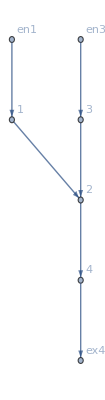

```mathematica
d2e["FG"]
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->80,I2->30,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}]])//AbsoluteTiming
```

Variables are all set

CleanEqualities for the values at the auxiliary edges

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the (non) critical case equations

CCS2: EliminateVarsSimplify for the us

CCS2: Finished with the us!

CCS2: Finished with the js!

{0.057643,<|u1→206,u2→126,u3→125,u4→15,u5→156,u6→126,u7→15,u8→15,u9→206,u10→206,u11→156,u12→156,j1→0,j2→80,j3→0,j4→110,j5→0,j6→30,j7→0,j8→110,j9→0,j10→80,j11→0,j12→30|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,0,1},{0,1,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{3,I2}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,I2->30,U1->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: After NewReduce, the system is:
jt419==0&&jt422==0&&u428==206&&u429==125&&u430==156
and the rules are:
<|j408→80,j409→30,u437→15,j404→80,j405→110-jt419-jt422,j406→30,j407→110-jt419-jt422,j410→0,j411→-jt419-jt422,j412→0,j413→-jt419-jt422,j414→0,j415→0,jt416→0,jt417→80,jt418→80-jt419,jt420→-jt422,jt421→-jt419,jt423→30-jt422,jt424→0,jt425→30,jt426→110-jt419-jt422,jt427→-jt419-jt422,u431→15,u434→-80+u428,u435→-110+u429,u436→-30+u430,u438→u428,u439→u430,u432→u428,u433→u430|>

DataToEquations: It took 0.027854 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.044755,Null}

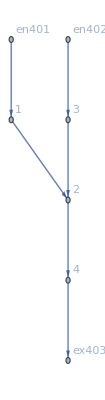

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j404→80,j405→110,j406→30,j407→110,j408→80,j409→30,j410→0,j411→0,j412→0,j413→0,j414→0,j415→0,jt416→0,jt417→80,jt418→80,jt419→0,jt420→0,jt421→0,jt422→0,jt423→30,jt424→0,jt425→30,jt426→110,jt427→0,u428→206,u429→125,u430→156,u431→15,u432→206,u433→156,u434→126,u435→15,u436→126,u437→15,u438→206,u439→156|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.98128×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.98128×10^-17

<|j404→80,j405→110,j406→30,j407→110,j408→80,j409→30,j410→0,j411→0,j412→0,j413→0,j414→0,j415→0,jt416→0,jt417→80,jt418→80,jt419→0,jt420→0,jt421→0,jt422→0,jt423→30,jt424→0,jt425→30,jt426→110,jt427→0,u428→21.2696,u429→17.6876,u430→20.9223,u431→15,u432→21.2696,u433→20.9223,u434→18.6876,u435→15.,u436→18.6876,u437→15,u438→21.2696,u439→20.9223|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.0483×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→22.5012,u522→18.3398,u523→21.9562,u524→15.,u525→22.5012,u526→21.9562,u527→19.3398,u528→15.,u529→19.3398,u530→15.,u531→22.5012,u532→21.9562|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.33236×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→26.5193,u522→20.4954,u523→25.2394,u524→15.,u525→26.5193,u526→25.2394,u527→21.4954,u528→15.,u529→21.4954,u530→15.,u531→26.5193,u532→25.2394|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.6479×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→119.768,u522→73.8023,u523→94.399,u524→15.,u525→119.768,u526→94.399,u527→74.8023,u528→15.,u529→74.8023,u530→15.,u531→119.768,u532→94.399|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.57004×10^-13,ComplexInfinity]

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→206.,u522→125.,u523→156.,u524→15.,u525→206.,u526→156.,u527→126.,u528→15.,u529→126.,u530→15.,u531→206.,u532→156.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.07055×10^-16

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→953.896,u522→588.99,u523→680.535,u524→15.,u525→953.896,u526→680.535,u527→589.99,u528→15.,u529→589.99,u530→15.,u531→953.896,u532→680.535|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 3.49007×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→76976.9,u522→54135.4,u523→55830.9,u524→15.,u525→76976.9,u526→55830.9,u527→54136.4,u528→15.,u529→54136.4,u530→15.,u531→76976.9,u532→55830.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.54095×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→1.18884×10^6,u522→898799.,u523→908526.,u524→15.,u525→1.18884×10^6,u526→908526.,u527→898800.,u528→15.,u529→898800.,u530→15.,u531→1.18884×10^6,u532→908526.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.87912×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→3.02767×10^11,u522→2.78714×10^11,u523→2.78731×10^11,u524→15.,u525→3.02767×10^11,u526→2.78731×10^11,u527→2.78714×10^11,u528→15.,u529→2.78714×10^11,u530→15.,u531→3.02767×10^11,u532→2.78731×10^11|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.48287×10^-17

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→8.5312×10^20,u522→8.47516×10^20,u523→8.47516×10^20,u524→15.,u525→8.5312×10^20,u526→8.47516×10^20,u527→8.47516×10^20,u528→15.,u529→8.47516×10^20,u530→15.,u531→8.5312×10^20,u532→8.47516×10^20|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.06128×10^-16

<|j497→80.,j498→110.,j499→30.,j500→110.,j501→80.,j502→30.,j503→0.,j504→0.,j505→0.,j506→0.,j507→0.,j508→0.,jt509→0.,jt510→80.,jt511→80.,jt512→0.,jt513→0.,jt514→0.,jt515→0.,jt516→30.,jt517→0.,jt518→30.,jt519→110.,jt520→0.,u521→5.23663×10^106,u522→3.03173×10^106,u523→3.85857×10^106,u524→15.,u525→5.23663×10^106,u526→3.85857×10^106,u527→3.03173×10^106,u528→15.,u529→3.03173×10^106,u530→15.,u531→5.23663×10^106,u532→3.85857×10^106|>